fermi function

```mathematica
k = 0.08617;
T = 4.2;
β=1/(k*T)
```

2.76309

```mathematica
f[x_]=1/(1+Exp[β x]); (*fermi function*)
```

Smearing Width

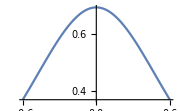

```mathematica
p[x_]:=-f'[x];
Plot[p[x],{x,-1/Sqrt[β],1/Sqrt[β]},ImageSize->Small,PlotRange->All]
```

measure of width of fermi distribution

```mathematica
w=5*π/(β Sqrt[3]);
```

Plots

```mathematica
Clear[range,plotrange]
```

```mathematica
range[e_,v_,w_]:=Flatten[{e,Sort[{-v - 3 w, -v + 3 w, -3 w, 3 w}]}]
plotrange[e_,v_,w_]:=Flatten[{e,MinMax[{-v - 3 w, -v + 3 w, -3 w, 3 w}]}]
integrand[e_,0.]:=0
integrand[e_,v_]:=n[e] n[e+v](f[e]-f[e+v])
```

```mathematica
plotintegrand[v_]:=Plot[integrand[e,v],plotrange[e,v,w],Frame->True,PlotLabel->"v="<>ToString[v],PlotRange->All,PlotPoints->200]
```

```mathematica
(*GraphicsGrid[Partition[Table[plotintegrand[v],{v,-11,11,2}],4],ImageSize->12*72]*)
```

```mathematica
Clear[n,e]
```

n(e) is the electronic density of states in the two metal strips.

```mathematica
i[0]=i[0.]=0.;(*special case for v=0*)
i[v_] := NIntegrate[n[e]n[e+v](f[e]-f[e+v]),range[e,v,w],WorkingPrecision->10, AccuracyGoal->10]
```

```mathematica
i[0]
```

0.

```mathematica
i[0.1]
```

NIntegrate::inumr: The integrand (1/(1+ⅇ^(2.76309 e))-1/(1+ⅇ^(2.76309 Plus[«2»]))) n[e] n[0.1+e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.946590747,-9.846590747}}.

NIntegrate[n[e] n[e+0.1] (f[e]-f[e+0.1]),range[e,0.1,w],WorkingPrecision→10,AccuracyGoal→10]

BCS DOS function

```mathematica
Clear[delta,gamma,z,e]
```

```mathematica
delta = 0.01;
gamma = 0.1;
z = e - I*gamma;
```

```mathematica
σ_bcs[e_] := Re[z]/(z^2-delta^2)^(1/2);
```

```mathematica
σ[v_] := NIntegrate[σ_bcs[e]*f'[e-v] ,{e,-5,5},WorkingPrecision->10, AccuracyGoal->10]
```

```mathematica
Show[Plot[σ[v],{v,-1.005,1.005},PlotRange->All],Frame->True,FrameLabel->{"meV","Normalized conductance(dIdV)"}]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in range[e,-1.00496].

NIntegrate::ilim: Invalid integration variable or limit(s) in range[e,-0.963939].

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

-Graphics-

Tabulating Integral and writing out the file

```mathematica
AbsoluteTiming[iv=Table[{v,i[v]},{v,-10,10,0.2}];] ;
```

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-10.+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,0.1534092534}}.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-9.8+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,-0.04659074661}}.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-9.6+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,-0.2465907466}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
outfilename:="Testdata beta DOS="<>ToString[β]<>" infile="<>infile<>" "<>DateString[Now]<>".TSV";
```

```mathematica
Export[outfilename,iv]
```

StringJoin::string: String expected at position 2 in Testdata beta DOS=2.76309 infile=<>infile<> Thu 10 Jun 2021 14:04:49.TSV.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-10.+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,0.1534092534}}.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-9.8+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,-0.04659074661}}.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-9.6+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,-0.2465907466}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Export::chtype: First argument Testdata beta DOS=2.76309 infile=<>infile<> Thu 10 Jun 2021 14:04:49.TSV is not a valid file specification.

$Failed

```mathematica
ListPlot[iv,PlotRange->All,Joined->True]
```

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-10.+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,0.1534092534}}.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-9.8+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,-0.04659074661}}.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^(2.76309 Plus[«2»]))+1/(1+ⅇ^(2.76309 e))) n[-9.6+e] n[e] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-9.846590747,-0.2465907466}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted